# 8

## PHAS2443: Practical Mathematics II Lecture 8: Monte Carlo methods

## Introduction

There are many applications in which events occur in a genuinely random way: examples from physics include the radioactive decay of a nucleus, the emission of an X-ray from an excited atom, or Brownian motion, whilst from other real-world problems we have the arrival of a car at the end of a queue of traffic -- or even the draw of a lottery ticket. There are also problems which have, on the face of it, no random element, but where we can get a useful answer by replacing the original problem with a random (or 'stochastic') one: even as well-determined a problem as the evaluation of an integral may yield to this approach. In all cases in which we use a stochastic approach, however, we need to apply some statistical techniques to obtain an idea of the accuracy of our solution.

## Computer-generated 'random numbers'

One key point to grasp is that what we call random numbers on a computer are in fact not random: they are determined by a completely deterministic algorithm, which starts from a 'seed' and generates a sequence from it. Often the seed is based on the date and time, so that different runs of the process produce different sequences, but if one starts from the same seed one will produce the same sequence. A great deal of research has gone into developing these algorithms for producing pseudorandom numbers, and ensuring that they satisfy a wide range of tests of randomness, but in the early days the algorithms had faults. A classic case was the randu random number generator, which was fine for one-dimensional problems but when successive terms in the sequence were used as the coordinates of points in a multi-dimensional space the points were found to lie on a series of lines in the plane. Most modern algorithms have been thoroughly tested: we will rely on the ones built into Mathematica,  for integers RandomInteger[], which can use a cellular automaton generator (Wolfram rule 30) amongst other, and for real numbers RandomReal[], which can use a so-called Marsaglia-Zaman subtract-with-borrow generator. Other methods can be selected by using the Method option of SeedRandom[]. The parallel Mersenne Twister method can generate 1024 independent sequences of period 2^4423-1!

A simple random number generator uses the following scheme to obtain the next number in the sequence from the present one, x:
    (a x + c) modulo m
with, usually, c set to zero and careful choice of a and m. By 'careful' is meant 'leading to a long sequence before a repetition'. One can easily see that a poor choice can be made, for example with a=12 and m=143 we have 
    x_2 = 12 x_1 modulo 143
x_3 = 12 x_2 modulo 143
      = 144 x_1 modulo 143
      = 144 x_1-143 *int((143 x_1+x_1)/143)
      = x_1
    leading to the unsatisfactorily short sequence of length 2!
    
    The randu scheme used m=2^31 and a=65539: here is an example of a scheme which shows the same sort of problems as randu.

seed=133
rn:=seed=Mod[65539 seed,2^25];
tt=Table[{rn,rn,rn,rn},{i,1,10000}];
Length[Union[tt]]
ListPlot[Transpose[Take[Transpose[tt],2]]]

133

10000

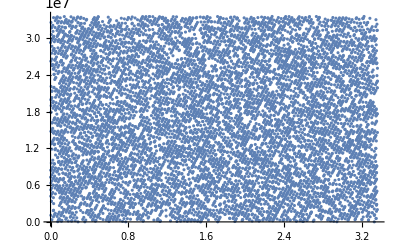

Modern algorithms perform much better that this: here is what Mathematica's built-in random number generator produces.

rn:=RandomInteger[{1,2^25}];
tt=Table[{rn,rn,rn,rn},{i,1,10000}];
Length[Union[tt]]
ListPlot[Transpose[Take[Transpose[tt],2]]]

10000

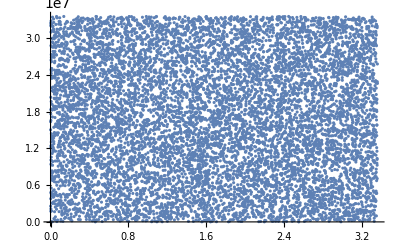

The standard methods return uniformly distributed random numbers -- that is, they are equally likely to lie anywhere within the specified interval. Often one wants numbers selected from some other distribution (commonly, the normal or Gaussian distribution, p(x) ∝ exp(-(x-μ)^2/2 σ^2) with mean μ and standard deviation σ). There are various ways of achieving this, depending on the form of the distribution one is trying to sample.  For a normal distribution, one can use the power of the central limit theorem, which tells us that the average of a large number of independent random numbers with well-defined mean and variance has a normal distribution. This suggests the following scheme:

norm[μ_,σ_,n_]:= Sum[RandomReal[{μ-Sqrt[3n] σ,μ+Sqrt[3n] σ}],{i,1,n}]/n
pp=Table[norm[1,1,10],{i,1,10000}];
Mean[pp]
StandardDeviation[pp]

1.00285

1.00283

#### Explanation

The aim is to produce random numbers centred on μ and with standard deviation σ. If we sample twice from a uniform distribution between μ-s and μ+s, with results x_1 and x_2, then the probability of getting a result 2x=(x_1+x_2) between x and x+δx (which must lie between μ-s and μ+s) is the area of a stripe in x_1-x_2 space:

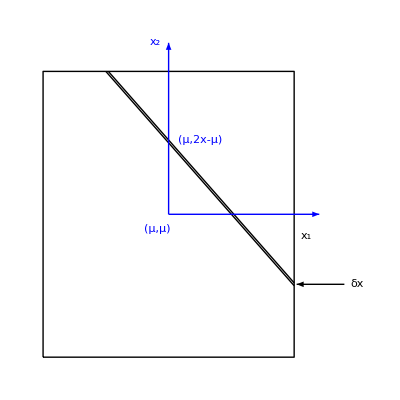

In other words, we can make x with a range of values of (x_1,x_2) from (2x-μ-s, μ+s) to (μ+s, 2x-μ-s) for μ≤ x≤ μ+s and from (μ-s,2x-μ+s) to (2x-μ+s,μ-s) for μ-s≤ x≤ μ. The probability p(x) for x between x and x+δx is proportional to the length of the diagonal strip equal to  2 √2(s-|x-μ|), defined only for μ-s≤ x≤ μ+s. Thus p(x) increases linearly from p(μ-s)=0  to p(μ)=2 √2 s, and decreasing linearly from p(μ)=2 √2 s to  p(μ+s)=0,  in simple words it is a triangular probability distribution centred on μ and with width 2s. If we move to higher dimensions there are similar results.
  For the two-dimensional case, the centred variance V can easily be calculated

```mathematica
p[x_]:=2Sqrt[2](s-Abs[x-μ]);
normval=Integrate[p[x],{x,μ-s,μ+s}];
u=Integrate[x p[x]/normval,{x,μ-s,μ+s}]
V=Simplify[Integrate[(x-u)^2 p[x]/normval,{x,μ-s,μ+s}],s>0]
```

μ

s^2/6

In order to get the same standard deviation of σ as the normal distribution, we need to set s = √6 σ (s = √(3n)σ for n=2).
  So our functions samples n times from a uniform distribution between μ-√(3n)σ and μ+√(3n)σ, and divide by n:

```mathematica
norm[μ_,σ_,n_]:=(∑_(i=1)^n RandomReal[{μ-√(3 n) σ,μ+√(3 n) σ}])/n
```

use the function to set up a table of 1000 samples from the resulting distribution

```mathematica
pp=Table[norm[1,1,10],{i,1,1000}];
```

and calculate the mean and standard deviation, which we see agree well with our target values.

```mathematica
Mean[pp]
StandardDeviation[pp]
```

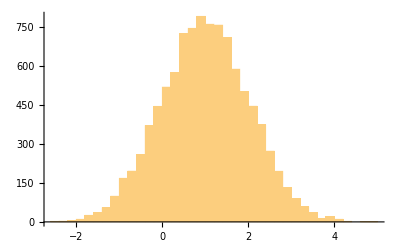

```mathematica
Histogram[pp,50]
```

This approach takes several evaluations of the uniformly distributed random number generator for each sample from the normal distribution. A more efficient method is the Box-Muller algorithm. The trick here bears some relationship to the method which is used to evaluate the integral of exp(-x^2), that is, to move into two independent dimensions. If the distribution functions for x and y each have the form 
p(x)=1/(√(2π)σ)exp(-x^2/2 σ^2) 
then the probability of finding x and y in the box of size (dx,dy) at (x, y) is p(x,y)dx dy=1/(2 π σ^2)exp(-(x^2+y^2)/(2 σ^2)) dx dy,
so that the probability of finding x and y in the annulus between r and r+dr (see figure)

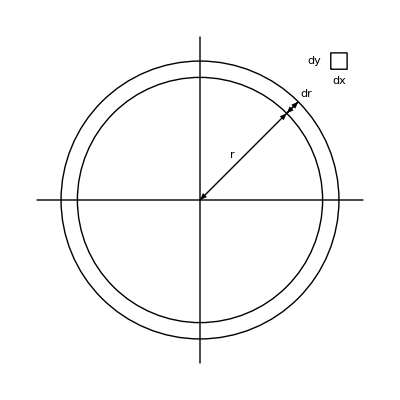

```mathematica
Show[Graphics[{Line[{{-2,0},{2,0}}],Line[{{0,-2},{0,2}}],Circle[{0,0},1.5],Circle[{0,0},1.7],Arrow[{{0.5,0.5},{0,0}}],Arrow[{{0.5,0.5},{1.5/(√2),1.5/(√2)}}],Arrowheads[Medium],Arrow[{{1.5/(√2),1.5/(√2)},{1.7/(√2),1.7/(√2)}}],Arrow[{{1.7/(√2),1.7/(√2)},{1.5/(√2),1.5/(√2)}}],Text["r",{0.4,0.55}],Text["dr",{1.3,1.3}],Line[{{1.6,1.6},{1.8,1.6},{1.8,1.8},{1.6,1.8},{1.6,1.6}}],Text["dx",{1.7,1.45}],Text["dy",{1.4,1.7}],BaseStyle->{FontSlant->"Italic"},BaseStyle->{FontSlant->"Italic"},BaseStyle->{FontSlant->"Italic"},BaseStyle->{FontSlant->"Italic"}}],AspectRatio->Automatic]
```

is given by changing to polar coordinates
2 π r p(r) dr = (2 π)/(2 π σ^2) exp(-r^2/2 σ^2) r dr,
and the probability of finding (x,y) between infinity and a distance R from the origin is
∫_R^∞ r/σ^2  exp(-r^2/2 σ^2)ⅆr =  exp(-R^2/2 σ^2) = p(R).
Now choose two uniformly distributed random numbers in the interval (0,1],t and u and define s such that s=t^2+u^2≤1,
in other words, reject the random numbers t and u if they do not satisfy this condition.  We can always find a value of R such that the area under the curve p(r)from R to infinity is s (since  0<s≤1), that is, 
R=σ √(-2  ln(s)),
a random point on the circle of radius R will give two independent random numbers from a normal distribution of standard deviation σ. Because of the way s was chosen we already have two random numbers which we can scale, to give
  t'=t σ √(-(2 ln(s))/s)  and  u'=u σ√(-(2 ln(s))/s).
  To test this out, we use the following code: 
 each call to sn generates two samples from a random distribution of unit standard deviation, which of course we can scale trivially to get any desired spread.

sn[]:=Module[{t,u,s=2},  
                           While[s>1,
                                      t=RandomReal[{-1,1}];
                                      u=RandomReal[{-1,1}];
                                      s=u^2+t^2
                                     ];
                          {t Sqrt[-2 Log[s]/s],u Sqrt[-2 Log[s]/s]}]

A test shows that the result is reasonable, giving a distribution that looks normal with the required variance.

1.0067

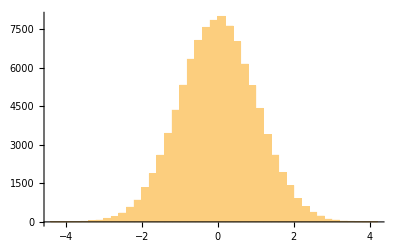

```mathematica
nn=Flatten[Table[sn[],{i,1,50000}]];
Variance[nn]
Histogram[nn,50]
```

Another approach to the generation of random variables, which applies when we cannot devise a simple transformation of variables as in the Box-Muller method, is the rejection method. Suppose the required distribution is p(x). We generate random numbers according to some distribution q(x) which need not be normalised (but should be normalisable, that is, have a finite integral over the domain of interest) with q(x)≥p(x) for all x -- ideally q(x) should be a distribution that has the same general shape as p(x), but in extremis we can just use a uniform distribution. This function q(x) is called the comparison function. The one thing we need to be able to do with q(x) is to generate samples from it (hence common choices are the uniform and the normal distribution) Then the procedure is as follows: we suppose that p(x) is represented by the red curve, and q(x) is the blue one.

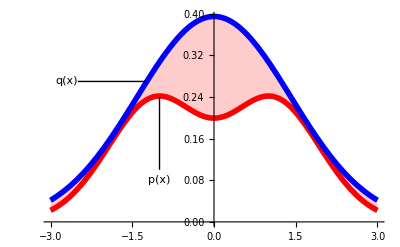

```mathematica
nn=∫_(-∞)^∞ ⅇ^(-x^2/4)ⅆx;
mm=∫_(-∞)^∞ (1+x^2) ⅇ^(-x^2/2)ⅆx;
p1=Plot[{((1+x^2) ⅇ^(-x^2/2))/mm,(1.4 ⅇ^(-x^2/4))/nn},{x,-3,3},PlotStyle->{{Thickness[0.01],RGBColor[1,0,0]},{Thickness[0.01],RGBColor[0,0,1]}},Filling->{1->{2}}];
p2=Graphics[{Line[{{-1,0.1},{-1,0.24}}],Text["p(x)",{-1,0.08}],Line[{{-2.5,0.27},{-1.26,0.27}}],Text["q(x)",{-2.7,0.27}]}];
Show[p1,p2]
```

a) Select a point from the distribution q(x). This gives a value of x.
b) Select a value y from a uniform distribution between 0 and q(x).
c) If y lies below p(x), accept the value of x, otherwise reject it.
d) Repeat until the required number of x values have been accumulated.
  Let's try this out: we will use the same example as in the sketch above:

p[x_]=(1+x^2) Exp[-x^2/2]/Integrate[(1+x^2) Exp[-x^2/2],{x,-∞,∞}]

(ⅇ^(-x^2/2) (1+x^2))/(2 √(2 π))

and the comparison function q(x) is

q[x_]=1.4  Exp[-x^2/4]/Integrate[ Exp[-x^2/4],{x,-∞,∞}]

0.394933 ⅇ^(-x^2/4)

which is a normal distribution, but widened and also scaled by 1.4 to ensure that it always lies above p(x).  As a check, we will generate samples from the normal distribution corresponding to our q(x):

NormalDistribution[0,√2]

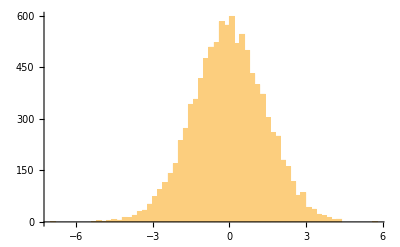

```mathematica
ndist=NormalDistribution[0,√2]
nd=Table[RandomVariate[ndist],{i,1,10000}];
Histogram[nd,50]
```

Now implement the rejection method.

7100

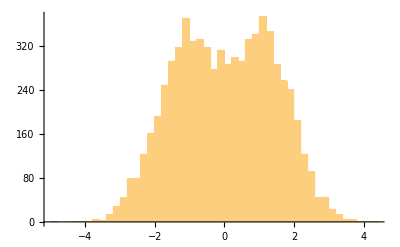

```mathematica
np=Table[xt=RandomVariate[ndist];If[RandomReal[{0,q[xt]}]<p[xt],xt,"null"],{i,1,10000}]//.{a___,"null",b___}->{a,b};
Length[np]
Histogram[np,50]
```

We can see that we are getting roughly the right shape, and we can see that the rejection rate is about 30%.

#### Explanation

Use Table to form a list of values from the distribution we define above (ndist)

```mathematica
np=Table[xt=RandomVariate[ndist];
```

then, using that sample value (xt), take a random number between 0 and q[xt],and store xt if that random number is less than p[xt]; otherwise store "null"

```mathematica
If[RandomReal[{0,q[xt]}]<p[xt],xt,"null"],
```

and do all that 10000 times.

```mathematica
{i,1,10000}]
```

Finally, clean up the list by deleting all the rejected cases, tagged by "null"

```mathematica
//.{a___,"null",b___}->{a,b};
```

The number of cases remaining out of our 10000 tries gives us an idea of the efficiency of the method. We also plot a histogram of the results.

```mathematica
Length[np]
Histogram[np]
```

## Monte Carlo integration

The basic idea behind Monte Carlo integration is to sample points at random within the integration domain, calculate the value of the integrand there, add up all the values, and multiply by a volume increment based on the average volume per sampling point used. But people have spent years devising schemes for evaluating integrals numerically, based on careful choices of sample points and weights which are selected to give perfect results for integrands which behave like high-order polynomials (Gaussian quadratures) -- why would we want to throw all that away? The answer is that those excellent algorithms simply cannot cope with integrals in spaces of very high dimensionality. For example, consider the particle problems that we were looking at in Lecture 7. If we have N particles interacting through potentials, a quantity which is important in statistical physics (see this term's PHAS2228 course) is the partition function, Z. This is related to the total energy E(r_1,r_2,r_3...r_N) by
     Z=∫∫∫...∫exp(-E(r_1,r_2,r_3... r_N)/k_BT) ⅆ r_1ⅆ r_2ⅆ r_3....ⅆ r_N,
  which, with N particles in a 3-dimensional space, is a 3N-dimensional integral. If we had 20 particles, and just selected 3 points in each dimension, this would involve 3^60 points, which even on a teraflop computer (one capable of carrying out 10^12 floating-point operations per second) would take over a billion years.
    The Monte Carlo approach is to say that the integral giving Z is just the average of exp(-E(r_1,r_2,r_3... r_N)/k_BT) multiplied by the volume of the space to the power N, so that if we take enough samples of the function to get a good estimate of the average we can find Z. In one dimension, we would write
    ∫_a^b f(x)ⅆx = (b-a) ⟨f(x)⟩,
    where ⟨⟩ denotes the average.
     We shall test the idea on a simple problem, using the Cauchy distribution:
     ∫_0^1 1/(1+x^2)ⅆx = π/4 = 0.78540.
     We shall generate a table showing how the value of the integral improves as we take more random samples. To do this, we shall run each sample size 10 times and calculate the standard deviation of the result. Note the factor of 1/n in the function mce: this represents the averaging process: in this case the range (b - a)=1.

mce[n_]:=Plus@@Table[1/(1+RandomReal[]^2),{i,1,n}]/n
stat[n_]:=Module[{t,mm,sd},
                                    t:=Table[mce[n],{i,1,10}];
                                    mm=Mean[t];
                                    sd=StandardDeviation[t];
                                   {mm,sd,Abs[mm-π/4]/sd}
                                  ]
TableForm[Table[Flatten[{10^i,stat[10^i]}],{i,1,4}],TableHeadings→{{},{"n","Mean","St Dev","Error/St Dev"}}]

| n | Mean | St Dev | Error/St Dev
 | 10 | 0.772534 | 0.0507251 | 0.253614
 | 100 | 0.780201 | 0.022637 | 0.229599
 | 1000 | 0.785726 | 0.006636 | 0.0494374
 | 10000 | 0.785111 | 0.00150827 | 0.190467

The standard deviation decreases as we increase the number of sample points, roughly as 1/√n.  There are statistical fluctuations, but the ratio of the error to the standard deviation does not alter much.

#### Explanation:

Start by defining the function mce to give the Monte Carlo estimate of the value of the integral using n sampling points. Note that as we want to evaluate the integral between 0 and 1 the default form of RandomReal will do. We form the summation by accumulating the values of the function at the sample points in a list, using Table, and then Applying Plus to the list, so that List[a,b,c...] becomes Plus[a,b,c...].

```mathematica
mce[n_]:=(Plus@@Table[1/(1+RandomReal[]^2),{i,1,n}])/n
```

Now investigate the statistics: for n sampling points, evaluate the integral 10 times, and calculate the mean and standard deviation of the results, as well as the discrepancy between the mean result and the exact result in units of the standard deviation.

```mathematica
stat[n_]:=Module[{t,mm,sd},
                                    t:=Table[mce[n],{i,1,10}];
                                    mm=Mean[t];
                                    sd=StandardDeviation[t];
                                   {mm,sd,Abs[mm-π/4]/sd}
                                  ]
```

Finally, display the results in a useful form for n taking the values 10, 100, 1000 and 10000.

```mathematica
TableForm[Table[Flatten[{10^i,stat[10^i]}],{i,1,4}],TableHeadings->{{},{"n","Mean","St Dev","Error/St Dev"}}]
```

We can do slightly better if we import an idea that we used in the rejection method for generating random numbers. Suppose we know some function g(x) which has a similar shape to the function we are trying to integrate, f(x), but which is normalised over the range a to b. Then we can rewrite the integral as
   ∫_a^b (f(x))/(g(x)) g(x) ⅆx,
   and change the variable from x to s where
     ds/dx = g(x)
     so
     s = ∫_a^x g(z)ⅆz
     and, because of the normalisation of g, the integral becomes
     ∫_0^1 (f(x(s)))/(g(x(s)))ⅆs
     and we evaluate this using uniform deviates over the range 0 to 1.  Obviously, we need to choose g so that the transformation back from s to x is tractable. If we choose 
       g(x) = 1/3(4-2x)
   this is a reasonable choice in terms of following f:

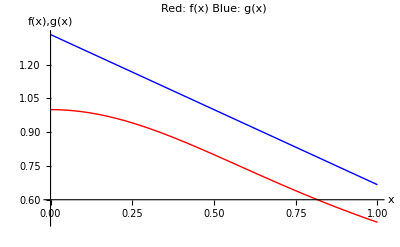

```mathematica
Plot[{1/(1+x^2),1/3 (4-2 x)},{x,0,1},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},PlotLabel->"Red: f(x)\nBlue: g(x)",AxesLabel->{"x","f(x),g(x)"}]
```

and is invertible:

```mathematica
sub=Solve[s==∫_0^x 1/3(4-2x)ⅆx,x][[1]]
```

{x→2-√(4-3 s)}

so that the integrand becomes

```mathematica
f[x]/g[x]/.{f[x]->1/(1+x^2),g[x]->1/3 (4-2 x)}/.sub
```

3/((4-2 (2-√(4-3 s))) (1+(2-√(4-3 s))^2))

mcet[n_]:=Plus@@Table[3/((4-2 (2-√(4-3 s))) (1+(2-√(4-3 s))^2))/.s→RandomReal[],{i,1,n}]/n
stat[n_]:=Module[{t,mm,sd},
                                    t:=Table[mcet[n],{i,1,10}];
                                    mm=Mean[t];
                                    sd=StandardDeviation[t];
                                   {mm,sd,Abs[mm-π/4]/sd}
                                  ]
TableForm[Table[Flatten[{10^i,stat[10^i]}],{i,1,4}],TableHeadings→{{},{"n","Mean","St Dev","Error/St Dev"}}]

| n | Mean | St Dev | Error/St Dev
 | 10 | 0.784788 | 0.008215 | 0.0743006
 | 100 | 0.785686 | 0.00244115 | 0.118103
 | 1000 | 0.785644 | 0.00060605 | 0.405724
 | 10000 | 0.785345 | 0.000266638 | 0.198047

The crucial point is that the standard deviation is much lower for a given n than with the unbiased sampling.

#### Explanation:

This is very similar to the previous version: all we have done is to alter the function to reflect the change of variables:

```mathematica
mcet[n_]:=1/n Plus@@Table[3/((4-2 (2-√(4-3 s))) (1+(2-√(4-3 s))^2))/.s->RandomReal[],{i,1,n}]
```

The only subtle point is the way we set up the table, where we have to ensure that the same random number appears in each position in the formula. Thus

```mathematica
1/((a+s) (b+s))/.s->RandomReal[]
```

1/((0.0275528+a) (0.0275528+b))

does what we want but

```mathematica
1/((a+RandomReal[]) (b+RandomReal[]))
```

1/((0.347962+a) (0.74067+b))

does not.

   The rest of the code is as before.

More generally, we can use the technique of importance sampling  with any probability distribution p(x) and estimate
∫_a^b (f(x))/(p(x)) p(x) ⅆx 
by taking N samples x_i from the distribution p(x) and evaluating
 1/N∑_(i=1)^N (f(x_i))/(p(x_i)).

We must stress, however, that the Monte Carlo is not a serious contender for one-dimensional integrals. It is much better to use one of the standard schemes (see the description of the algorithms used in NIntegrate for some of the names).  The important point, though, is that for a Monte Carlo scheme using n samples, the expected error varies as √(1/n). For a conventional scheme in d dimensions the same number of points, n/d, will be used in each dimension, and the error typically varies as some power of d/n, say (d/n)^α. This means that as the dimensionality d increases there comes a point at which the Monte Carlo method wins.

## Monte Carlo Simulation

As you have seen in this term's Thermal Physics course, the probability density of atomic-scale systems is controlled by the Boltzmann distribution.  Under conditions of a fixed large number of distinguishable particles in equilibrium at a temperature T, the probability of occupation of an energy level E_i will be given by
 p(E_i) := (exp(-E_i/(k_B  T)))/(∑_i exp(-E_i/(k_B  T))).

What is perhaps surprising is that the behaviour of systems can be modelled quite successfully with quite small numbers of particles.  Furthermore, the approach to equilibrium can be mimicked by the Monte Carlo method.  This method uses the computer's random number generator to simulate the exchanges of energy between particles which occur as the system approaches equilibrium, and was first used on the MANIAC computer at Los Alamos in the early 1950s (Metropolis, Rosenbluth, Rosenbluth, Teller and Teller, Journal of Chemical Physics, 21, 1087, 1953): it is often referred to as the Metropolis algorithm, after the first author.

The basic idea is to start with a random distribution of particles over energy levels, randomly pick a particle, randomly alter its energy level, and then evaluate the total energy.   If the energy is decreased as a result of the change, the change is accepted and one proceeds to the next random change.  The subtle point, though, is that if the energy is increased by the change, the change is not always rejected: instead another random number is picked, between 0 and 1, and if the energy change ΔE is such that exp(-ΔE/k_BT) is greater than this random number the new state is accepted even though it increases the energy.  The point of this is that it allows the system to ‘shake’ itself out of regions which are local minima of the energy surface, but not the global minimum.  It is clear that the higher the temperature T, the greater the probability of accepting an 'uphill jump'.

To make the 'system', 'particles' and 'energy levels' take on some meaning, let us consider the Ising model. This is probably one of the most widely studied of model systems, and although it was originally applied to magnetic systems (and this is the approach we shall follow) it is equally applicable to metallic alloys, the growth of solids from vapour, and other problems. The form of the Ising model which we use assumes that atoms with unpaired electrons are arranged on a square lattice, and that the energy of the whole system is given by 
           E = -∑_(i,j=i)^N J_ij s_i.s_j-∑_(i=1)^n m B.s_i,
 The coupling constant J_ij represents a quantum mechanical exchange interaction between the spins (not a classical magnetic dipole-dipole interaction between their magnetic moments, which would be far too weak an effect to account for phenomena such as ferromagnetism which the Ising model seeks to explain).  We shall take J_ij to be zero unless i and j are nearest-neighbour sites of the square lattice, in which case it will be taken to have a constant value, J.  Note that as the energy expression is written, if J is positive it favours a parallel alignment of the spins.   The second term represents the interaction of the spins, magnetic moments m s, with an applied external field B.
           
In the simulations which follow, we take the spins to be 1/2, so that each has only two possible directions, and thus they interact:
  1. with each other with coupling constant J (the energy is lower if two neighbouring spins are parallel than if they are antiparallel): in the simulation below J / (k_B T) is called joverkt,
  2. with an applied magnetic field: here the key quantity is the ratio B m / (k_B T), boverkt.

In the Monte Carlo Ising simulation one must:
  1.  Set up random arrangement of spins,
  2.  Pick a spin at random,
  3.  Calculate the energy change arising from reversing that spin,
  4.  If the energy change is negative, OR on randomly selected but infrequent occasions when the energy change is positive, reverse the spin (this is to allow the system to skip out of local minima),
  5.  Keep going.
Note that the updates are done at random, sequentially, in the mesh -- we do not use a cellular automaton 'update all at once' approach.  
One more thing needs to be settled: the boundary conditions to be applied at the edges of the simulation.  Here we loop the system back on itself: that is, we use periodic boundary conditions.
Dependent on the settings of joverkt and boverkt, you will see the system keep up a random arrangement of spins, or align in blocks (even in zero external field - corresponding to a ferromagnetic state). The degree of long-range order (which is just the average of the spin over the whole system) is monitored and plotted at the end.

We now define some parameters of the simulation.The maximum number of Monte Carlo steps (i.e. changes of spin) is maxstep. A two-dimensional diagram of the distribution of spins will be plotted every Ising Monte Carlo steps. Probably five such diagrams will be enough to allow us to follow the evolution of the system, so set gstep to maxstep/5. We would like to see how the amount of order in the system changes as it evolves. To do this we save the order parameter every lostep steps.  We probably do not want more than 100 points in this graph, so choose lostep to be maxstep/100. We will also average the order, and record this average, the average energy, and the mean square deviation of the order, but we do not want to do this during the early stages, before the simulation has approached the equilibrium state.  Accordingly we begin to record these quantities after bstep steps, say after 9/10th of the simulation.

maxstep=10000;
bstep= 9 maxstep/10;
lostep=maxstep/100;
gstep= maxstep/10;

The next parameter, l, is going to have the largest influence on the length of time taken to run the simulation.  It is the number of spins along each side of the square lattice.  A choice of 50 should give an adequate result, but may take rather too long; anything less than 10 will be too small to be useful.

l=50;

We now define the physical parameters of the simulation.  Initially, we choose to have an external field (boverkt = 0.4) but no interactions between the spins (joverkt = 0.0).

boverkt=0.4;
joverkt=0.0;

Now begin by setting up the table ml with randomly placed value of +1 and -1.

f[x_]:=x (-1);
l2=l l;
SeedRandom[];
ml=Table[(-1.)^RandomInteger[{0,1}],{l},{l}];

Set up values to accumulate the energy, spin, and spin-squared. Calculate the initial average spin, and plot the initial spins.

```mathematica
ml[[1]]
```

{1,-1,1,-1,1,-1,1,-1,-1,-1,1,-1,-1,-1,1,1,-1,-1,-1,-1,1,1,-1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,-1,1,1,-1,1,1,-1,-1,-1,-1,1,1,1,-1,1}

sume=0;
summ=0;
summ2=0;
etot=0;
longorder=Abs[Apply[Plus,Flatten[ml]]/l2];
gra=MatrixPlot[ml,Mesh->False]

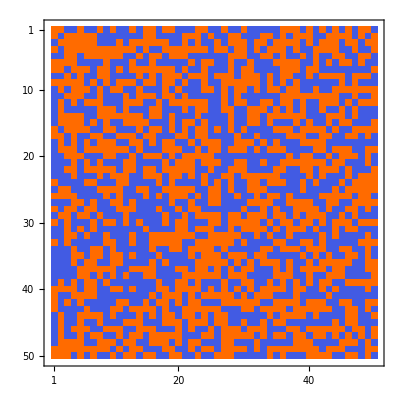

Now pick random points in the mesh (i1,i2), calculate the total spin of the neighbours dg (applying periodic boundary conditions), and the change of energy (in units of k_B T) de associated with flipping the spin at (i1,i2). If this energy change is negative, make the flip. If the energy change is positive accept the flip with probability exp(-de).  Accumulate the results, plot the graphs.

Do[
	    i1=RandomInteger[{1,l}];
	    i2=RandomInteger[{1,l}];
	    j1=i1+1;j2=i2+1;k1=i1-1;k2=i2-1;
	    If[j1>l,j1=1];If[j2>l,j2=1];
	   If[k1<1,k1=l];If[k2<1,k2=l];
	   dg= ml[[j1,i2]]+ml[[k1,i2]]+ml[[i1,j2]]+ml[[i1,k2]];
	   etot=
		    etot-joverkt dg ml[[i1,i2]]-boverkt ml[[i1,i2]];
	   de=-2 f[ml[[i1,i2]]] (joverkt dg + boverkt);
	   dw=N[Exp[-de]];
	  If[dw<1 && dw>RandomReal[] || de<0,
		       ml[[i1,i2]]=-ml[[i1,i2]]
		    ];
	  mm=Apply[Plus,Flatten[ml]]/l2;
	  If[Mod[i,lostep]==0,
		       longorder=Flatten[{longorder,
					Abs[mm]}]
		    ];
	  If[Mod[i,gstep]==0,
		      Print[MatrixPlot[ml,
				         Mesh->False,
				         PlotLabel->StringForm["Iteration number ``",i]
		                 ]
	      ]];
		If[i>bstep,
		     summ=summ+mm;
			   summ2=summ2+mm mm;
			   sume=sume+etot],
  	{i,1,maxstep}
 ]
Print[ListPlot[longorder,PlotRange→All,
	Joined->True,PlotLabel->"Long-range order parameter"]];
summ2=Sqrt[summ2/(maxstep-bstep)-(summ/(maxstep-bstep))^2];
		summ=summ/(maxstep-bstep);
		sume=sume/(maxstep-bstep);
		Print[StringForm["l=``  boverkt=``  joverkt=`` run for `` steps",l,boverkt,joverkt,maxstep]];
			Print[StringForm["RMS spin deviation = ``",N[summ2]]];
			Print[StringForm["Mean spin = ``",N[summ]]];
				Print[StringForm["Mean energy = ``",N[sume]]];

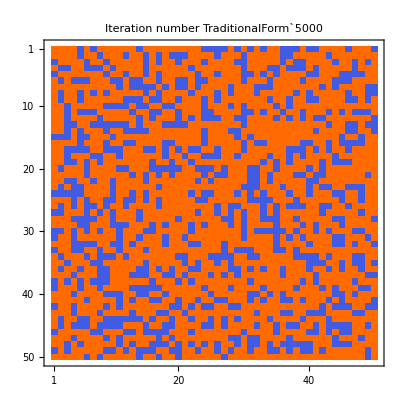

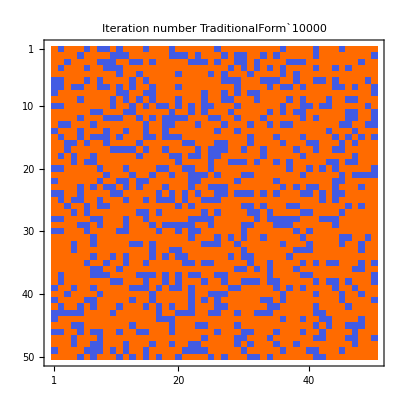

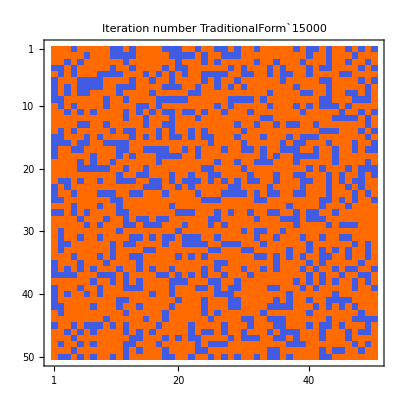

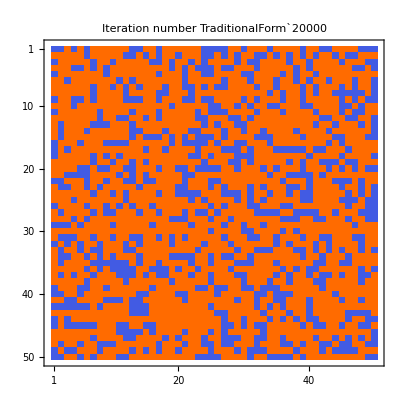

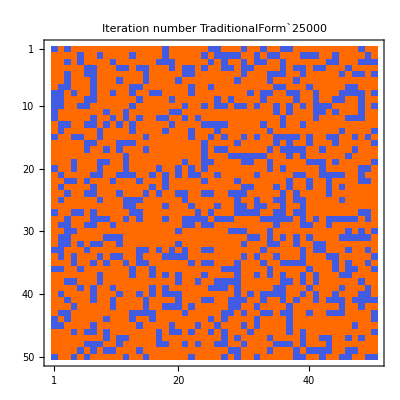

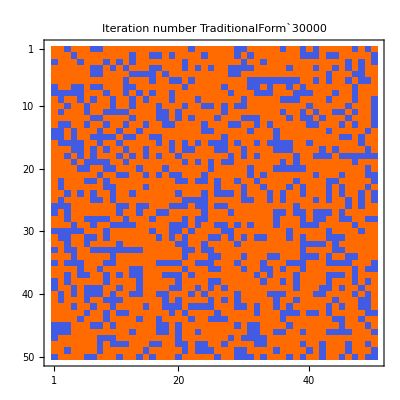

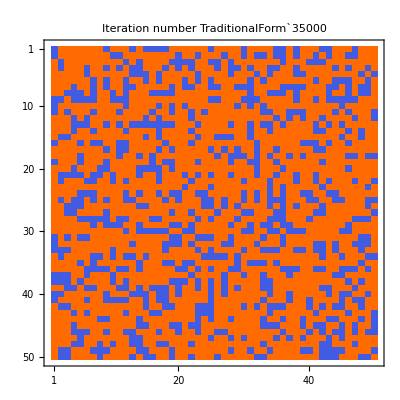

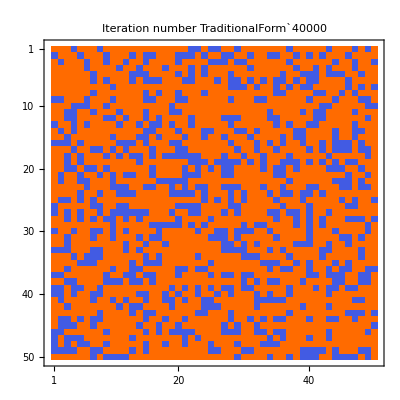

l=50  boverkt=0.4  joverkt=0. run for 50000 steps

RMS spin deviation = 0.0139228

Mean spin = 0.355194

Mean energy = -7008.57

Mean energy = -6975.1

What we see is that the pattern remains fine-grained, but that more spins are aligned in one direction than the other.

#### Explanation

When we tease the code apart (and this is the longest chunk of code we have met on the course so far), this is how it works.
   We set up a Do loop, and start by selecting a cell (i1,i2) at random and locating the cells above (k1=i1-1,i2), below (j1=i1+1,i2), to the left (i1,k2=i2-1) and to the right (i1,j2=i2+1)

```mathematica
Do[
	    i1=RandomInteger[{1,l}];
	    i2=RandomInteger[{1,l}];
	    j1=i1+1;j2=i2+1;k1=i1-1;k2=i2-1;
	    If[j1>l,j1=1];If[j2>l,j2=1];
	   If[k1<1,k1=l];If[k2<1,k2=l];
```

where we have taken care over what happens at the edges, imposing periodic boundary conditions. Now form the sum of the spins on the neighbours, dg, and calculate the contribution to the total energy and the energy change, de, which would arise if spin (i1,i2) were flipped.

```mathematica
dg= ml[[j1,i2]]+ml[[k1,i2]]+ml[[i1,j2]]+ml[[i1,k2]];
	   etot=
		    etot-joverkt dg ml[[i1,i2]]-boverkt ml[[i1,i2]];
	   de=-2 f[ml[[i1,i2]]] (joverkt dg + boverkt);
```

Now accept the change if it reduces the energy, or (with reduced probability) of it increases the energy slightly.

```mathematica
(dw=N[ⅇ^-de];) (If[(dw<1&&dw>RandomReal[])||de<0,ml⟦i1,i2⟧=-ml⟦i1,i2⟧];)
```

Calculate a long-range order parameter, the total spin, and accumulate values in longorder: only do this every lostep updates.

```mathematica
mm=Apply[Plus,Flatten[ml]]/l2;
	  If[Mod[i,lostep]==0,
		       longorder=Flatten[{longorder,
					Abs[mm]}]
		    ];
```

Every gstep updates, display the spin distribution (Note that as we are inside a loop we have to force Mathematica to show the graph by using Print).

```mathematica
If[Mod[i,gstep]==0,
		      Print[MatrixPlot[ml,
				         Mesh->False,				           PlotLabel->StringForm["Iteration number ``",i]]
		                 ]
	      ];
```

Every bstep updates, save the total spin, total spin squared, and total energy.

```mathematica
If[i>bstep,
		     summ=summ+mm;
			   summ2=summ2+mm mm;
			   sume=sume+etot],
```

Do all that maxstep times.

```mathematica
{i,1,maxstep}
 ]
```

Having finished, plot the time evolution of the long range order, and the averages and deviations of the spins, and the average energy.

```mathematica
Print[ListPlot[longorder,Joined->True,PlotLabel->"Long-range order parameter"]]
summ2=√(summ2/(maxstep-bstep)-(summ/(maxstep-bstep))^2);
summ=summ/(maxstep-bstep);
sume=sume/(maxstep-bstep);
Print["l=\!\(l\)  boverkt=\!\(boverkt\)  joverkt=\!\(joverkt\) run for \!\(maxstep\) steps"];
Print["RMS spin deviation = \!\(summ2\)"];
Print["Mean spin = \!\(summ\)"];
Print["Mean energy = \!\(sume\)"];
```

What we can see is that the order parameter (that is, the average spin longorder) oscillates around a value of about 0.4. When you cover the theory of magnetic systems you will be able to confirm that the expected average is tanh(boverkt),

```mathematica
Tanh[boverkt]
```

0.379949

so our result is reasonable.

We now consider a more complicated problem: a phase transition.  You are probably aware that if a ferromagnetic material is heated to a high temperature, it ceases to be ferromagnetic (that is, it ceases to have a permanent magnetic dipole moment).To demonstrate this with our model, we should remove the external field (set boverkt to 0) and introduce the spin-spin interaction (set up a non-zero value of joverkt - try values between 0.1 and 5.0).  We can look at the graph of order against step number to judge whether the system has finished changing in a systematic way and is merely jumping about the equilibrium, and we can look at the two-dimensional plots to get an idea of the way the local order develops.  We'll use a larger mesh here, 100 by 100 and joverkt parameters of 0.1 and 2.0.  We'll just repeat the block of code from above here, as we did not set it up as a function (which might have been more tidy).

l=100;
maxstep=50000;
bstep= 9 maxstep/10;
lostep=maxstep/100;
gstep= maxstep/10;
boverkt=0.0;
joverkt=2.0;
ml=Table[(-1.)^RandomInteger[{0,1}],{l},{l}];
sume=0;
summ=0;
summ2=0;
etot=0;
longorder=Abs[Apply[Plus,Flatten[ml]]/l2];
gra=MatrixPlot[ml,Mesh->False];
Do[
	    i1=RandomInteger[{1,l}];
	    i2=RandomInteger[{1,l}];
	    j1=i1+1;j2=i2+1;k1=i1-1;k2=i2-1;
	    If[j1>l,j1=1];If[j2>l,j2=1];
	   If[k1<1,k1=l];If[k2<1,k2=l];
	   dg= ml[[j1,i2]]+ml[[k1,i2]]+ml[[i1,j2]]+ml[[i1,k2]];
	   etot=
		    etot-joverkt dg ml[[i1,i2]]-boverkt ml[[i1,i2]];
	   de=-2 f[ml[[i1,i2]]] (joverkt dg + boverkt);
	   dw=N[Exp[-de]];
	   If[dw<1 && dw>RandomReal[] || de<0,
		       ml[[i1,i2]]=-ml[[1,i2]]
		    ];
	  mm=Apply[Plus,Flatten[ml]]/l2;
	  If[Mod[i,lostep]==0,
		       longorder=Flatten[{longorder,
					Abs[mm]}]
		    ];
	  If[Mod[i,gstep]==0,
		      Print[MatrixPlot[ml,
				         Mesh->False,
				         PlotLabel->StringForm["Iteration number ``",i]]
		                 ]
	      ];
		If[i>bstep,
		     summ=summ+mm;
			   summ2=summ2+mm mm;
			   sume=sume+etot],
  	{i,1,maxstep}
 ]
Print[ListPlot[longorder,PlotRange→All,
	Joined->True,PlotLabel->"Long-range order parameter"]];
summ2=Sqrt[summ2/(maxstep-bstep)-(summ/(maxstep-bstep))^2];
		summ=summ/(maxstep-bstep);
		sume=sume/(maxstep-bstep);
		Print[StringForm["l=``  boverkt=``  joverkt=`` run for `` steps",l,boverkt,joverkt,maxstep]];
			Print[StringForm["RMS spin deviation = ``",N[summ2]]];
			Print[StringForm["Mean spin = ``",N[summ]]];
				Print[StringForm["Mean energy = ``",N[sume]]];

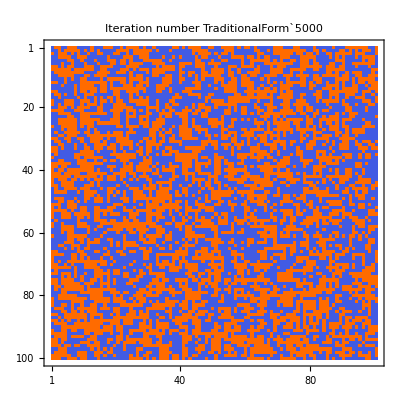

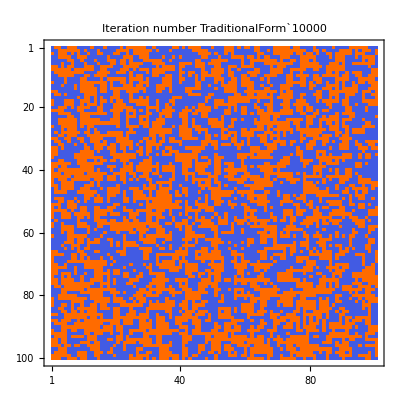

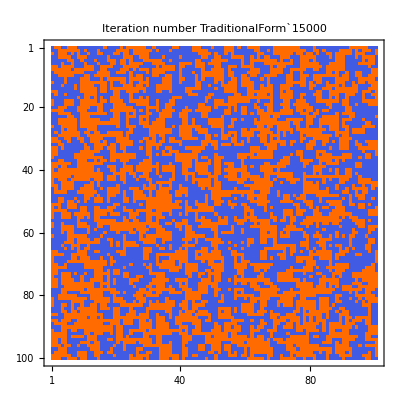

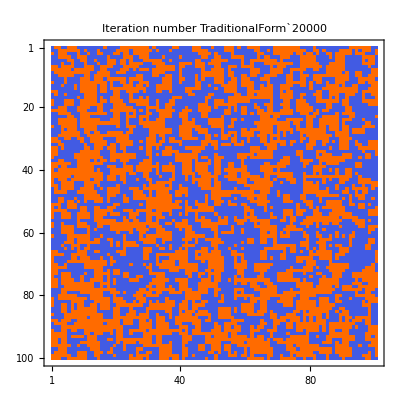

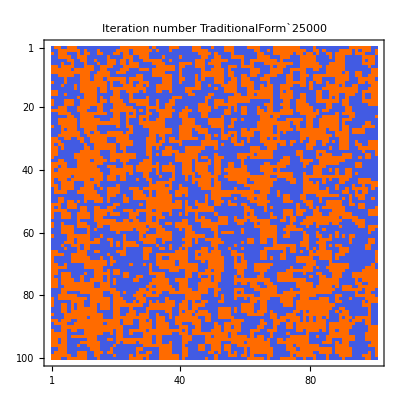

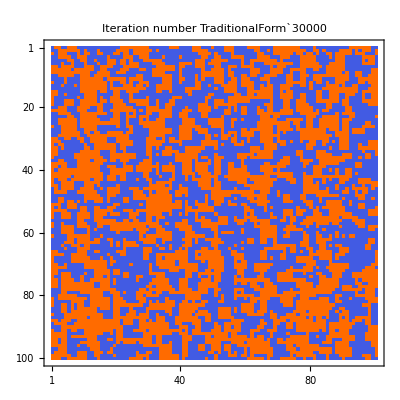

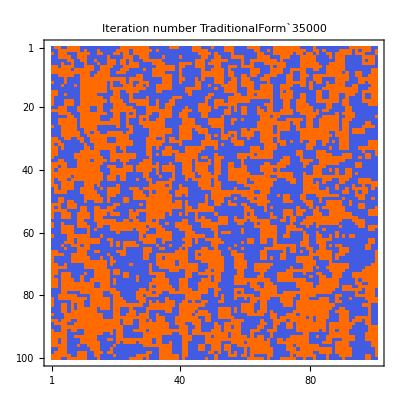

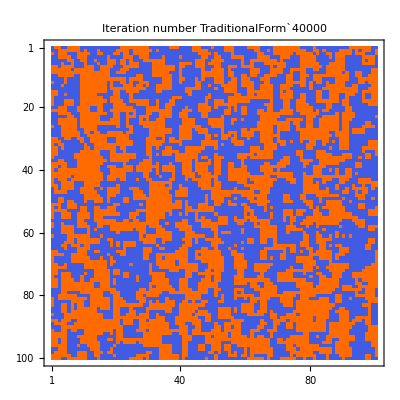

l=100  boverkt=0.  joverkt=2. run for 50000 steps

RMS spin deviation = 0.00114886

Mean spin = 0.165565

Mean energy = -129366.

We find that the interactions lead to 'domains' in which the spins are all parallel -- as shown by the 'blocky' nature of the image -- but in the absence of any applied field there are as many domains with spin up as spin down. This order-disorder transition should set in, for this two-dimensional structure, at a value of joverkt of 0.44. The bigger we make this parameter the clearer the blocks become. The essence of an order-disorder transition of this kind is that one should see 'patches' of order at all length scales. To model it properly needs large regions, and special techniques to overcome what is called 'critical slowing down' -- the fact that the system changes very slowly close to the critical point.

## The Metropolis algorithm for minimisation

A very common problem in physics and in other walks of life is that of finding the minimum of some function. In a scientific application we might be trying to find the equilibrium, minimum energy, configuration of a system. In a commercial environment, we might want to find the shortest path joining a number of points (the so-called travelling salesman problem). These are very complicated problems, and it is fair to say that, except for very simple cases, there is no method that is guaranteed to find the global minimum. Simple algorithms simply try to go downhill all the time: in a case such as the one shown below that will find the minimum if it starts from point A, but only a local minimum if started from B (and that is assuming that there is no deeper minimum off the screen).

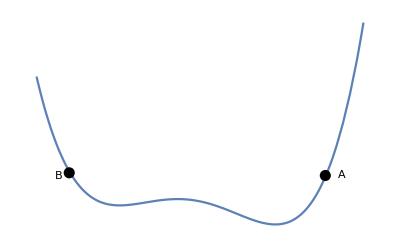

```mathematica
pp=Plot[3 x^4-5 x^3+x-2,{x,-1,2},Axes->False];
gg=Graphics[{PointSize[0.02],Point[{-0.7,-0.35}],Point[{1.65,-0.5}],Text["B",{-.8,-0.5}],Text["A",{1.8,-0.48}]}];
Show[pp,gg]
```

The ideas of the Metropolis algorithm are based on ideas of how liquids cool and solidify. At high temperatures the atoms have a lot of energy, and move around freely. If they are cooled slowly, they have time to explore lots of different relative positions and can settle down into regular structures - crystals. If they are cooled too quickly they can get trapped in positions which are not optimal, but they would require some thermal energy to jump out of those positions into somewhere better. This is what happens if a liquid is cooled quickly, and forms a glass -- it is in a metastable state, rather than the ground state. This is not unique to glasses: substances which can take on several crystal forms can get 'stuck' in forms which are not thermodynamically the most stable. This is the case with diamond, the stable form of which is graphite. 

  So what is done in a Metropolis minimisation is to run Monte Carlo simulations, but gradually decrease the control temperature (this temperature control is called the 'annealing schedule', by analogy of the use of temperature control in annealing defects out of metals). The exact details of how best to do this are hard to optimise.

## Summary

This lecture has only skimmed the surface of Monte Carlo methods. These techniques have been the subject of an enormous amount of research, which has led to their application in a huge range of areas. Other applications include the growth of crystal grain structures in solids (which use methods very similar to the Ising model), and crystal growth from a seed in a crystal (including the prediction of dendritic, tree-like, growth structures, as is followed in one of the miniprojects). They can also be used to solve differential equations, where instead of applying a finite difference formula such as (for steady-state heat flow, with the temperature at spatial position (i,j) and heat input Q_(i,j) at position (i,j) - see Homework 2)
   θ_(i,j) = 1/4{θ_(i+1,j)+θ_(i-1,j)+θ_(i,j+1)+θ_(i,j-1)}+Δx^2/κ Q_(i,j)
   directly we take 
    θ_(i+1,j)+Δx^2/(4κ)Q_(i,j),  θ_(i-1,j)+Δx^2/(4κ)Q_(i,j), θ_(i,j+1)+Δx^2/(4κ)Q_(i,j) and  θ_(i,j-1)+Δx^2/(4κ)Q_(i,j)
as estimators of the temperature θ_(i,j), each with probability 0.25. A point is picked at random, its temperature updated, then one of its neighbours is picked and updated, and the process is repeated until a boundary (at known temperature) is reached. If this process is repeated a large number of times from different starting points a solution will be approached. This is, basically, a 'random walk' process, and works because of the diffusive nature of heat flow.

Note that several of the examples in this lecture have been taken from An Introduction to Computer Simulation by M.M. Woolfson and G.J. Pert (Oxford 1999).

A.H. Harker
Physics and Astronomy, UCL
September 2005; updated February 2007, February 2008, February 2009, February 2010.
Amended by Patrick Guio, Physics and Astronomy, UCL, March 2015, March 2016.
Minor amendment by N. A., March 2017